## Propeller

```mathematica
<<C:\\Hopsan\Compgen\CompgenNG.mx
```

```mathematica
path=ToFileName[{"C:","HopsanTrunk","ComponentLibraries","defaultLibrary","Special","AeroComponents"}];
```

Model of propeller

```mathematica
domain="Aero";
displayName="Propeller";
brief="Model of a propeller";
componentType="ComponentC";
author="Petter Krus <petter.krus@liu.se>";
affiliation = "Division of Fluid and Mechatronic Systems, Linköping University";
SetFilenames[path,domain,displayName];
ResetComponentVariables[];
Date[]
```

{2015,2,12,20,22,1.61384}

```mathematica
inputVariables={
{Up,1.25,double,"m/s","Air speed"},
{rho,1.25,double,"kg/m3","Air density"}
};
```

```mathematica
k=.;
dp=.;
cp=.;
b1=.;
b2=.;
```

```mathematica
inputParameters={
{dp,1.,double,"m","Propeller diameter"},
{b1,0.2,double,"","Propeller thrust coefficient"},
{b2,0.2,double,"","Propeller thrust coefficient"},
{g1,0.205,double,"","Propeller torque coefficient"},
{g2,0.2,double,"","Propeller torque coefficient"},
{ct0,0.12,double,"","Propeller torque coefficient"},
{cp0,0.08,double,"","Propeller torque coefficient"},
{k,4,double,"","exponent for transition"}
};
```

```mathematica
outputVariables={
{thrust,500.,double,"N","Thrust"},
{torque,0.,double,"N","Torque"},
{Pin,0.,double,"W","Input power"},
{Pout,0.,double,"W","Output Power"},
{Jp,0.,double," ","Advance rate"}
};
```

```mathematica
nodeConnections={
MechanicRotCnode[mr1,0.,0.,"Mechanical rot.connection"]
};
```

```mathematica
b1=.;
b2=.;
g1=.;
g2=.;
ct0=.;
cp0=.;
k=.;
```

```mathematica
ct1=b1-b2 Jpe;
cp1=g1-g2 Jpe;
```

```mathematica
ct:=ct1/Abs[ct1](1/((1/ct0)^k+1/Abs[ct1]^k))^(1/k);
cp:=cp1/Abs[cp1](1/((1/cp0)^k+1/Abs[cp1]^k))^(1/k);
```

```mathematica
b1=0.2;
b2=0.2;
g1=0.205;
g2=0.2;
ct0=0.12;
cp0=0.08;
k=3;
Jpe=.;
```

The trust and power coefficients are plotted below. The curves are symetric although in reality the curves are different abouve Jpe = 1. The normal mode of operation is however, with positive coefficients. The behavior here would be accurate  with a symetric profile.

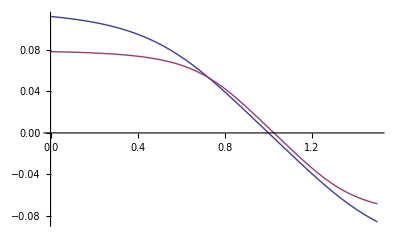

```mathematica
Plot[{ct,cp},{Jpe,0,1.5}]
```

```mathematica
b1=.;
b2=.;
g1=.;
g2=.;
ct0=.;
cp0=.;
k=.;
```

```mathematica
ct
```

((b1-b2 Jpe) (1/((1/ct0)^k+Abs[b1-b2 Jpe]^-k))^(1/k))/Abs[b1-b2 Jpe]

```mathematica
cp
```

((g1-g2 Jpe) (1/((1/cp0)^k+Abs[g1-g2 Jpe]^-k))^(1/k))/Abs[g1-g2 Jpe]

```mathematica
nmp=60 wmr1/(2 pi)
```

(30 wmr1)/pi

```mathematica
nsp=wmr1/(2 pi)
```

wmr1/(2 pi)

```mathematica
Jpe=Up/((.00001+nsp) dp)
```

Up/(dp (0.00001+wmr1/(2 pi)))

```mathematica
systemEquationsDA={
thrust==ct rho nsp^2 dp^4,
cmr1==(cp rho nsp^2 dp^5)/(2 pi)
};
```

```mathematica
systemVariables={thrust,cmr1}
```

{thrust,cmr1}

```mathematica
expressions={
torque==cmr1,
Zcmr1==(cp dp^5 rho wmr1)/(4 pi^3)mTimestep,
Pin==cmr1 wmr1,
Pout==thrust Up,
Jp==Jpe
};
```

```mathematica
Compgen[file]
```

Unset::wrsym: Symbol Up is Protected.

XMLElement::cntsList: XMLElement["modelobject", {"typename" → "AeroPropeller", "" … "e" → "" … ""}, {XMLElement["icon", {"isopath" → "AeroPropeller.svg", "iconrotation" → "ON", "userpath" → "AeroPropeller.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → "0", "y" → 0.5, "a" → "0", "name" → "Pmr1"}, {}], « 6 », XMLElement["portpose", {"x" → "0.833333", "y" → "1", "a" → "90", "name" → "Jp"}, {}]}]}] in XMLElement[« 1 »] is not a list of contents. The third item in an XMLElement must be a list of contents, even if it is an empty list.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.5 in "y" → 0.5 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.333333 in "x" → 0.333333 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

General::stop: Further output of Export :: autofix will be suppressed during this calculation.

XMLElement::attrhs: 0.666667 in "x" → 0.666667 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

General::stop: Further output of XMLElement :: attrhs will be suppressed during this calculation.